## Usage + Global Functions and Variables

This file was created with Mathematica/10.2 and can only be claimed to work (at most) on such a system. 

Prior to analysis you must :
(1) Run the simulations (see versatile_framework_paper/README.md)
(2) Postprocess: 
In most cases this means converting the human-readable-output of the simulation to something easier for mathematica to read. My solution was a “dat” file. The python script versatile_framework_paper/python/txt2dat.py converts the txt files from the simulation output to dat files that mathematica can import easily using the pts function, below.
Example Usage:
python versatile_framework_paper/python/txt2dat.py test actins
generates the file test/txt_stack/actins.dat from the file test/txt_stack/actins.txt. 
For most of the analyses below, this must be done for the links file and sometimes the actins file. 

For figures 2, 3D, 7C-D and S4 there are separate pre/post processing requirements; see there for details.

### Set your Directories Here

```mathematica
outdir="/project/weare-dinner/simonfreedman/cytomod/out";
fig1dir=outdir<>"/minimal_actomyosin/";
fig2dir=outdir<>"/profiling/";
fig3dir=outdir<>"/pl/";
fig5dir=outdir<>"/shear/";
fig6dir=outdir<>"/motility/";
fig7dir=outdir<>"/contracting/dens_dens_new/kon1_dt2e-5/mdens0.20_xldens1.0/";
```

### Loading Data

```mathematica
ClearAll[pts,pts3];
pts[dir_,name_]:=
If[
FileExistsQ[dir<>"/txt_stack/"<>name<>".dat"],
ToExpression[Import[dir<>"/txt_stack/"<>name<>".dat","TSV"]],
Print[dir<>"/txt_stack/"<>name<>".dat doesn't exist"];{}
];
pts3[dir_,name_]:=Map[Internal`StringToDouble/@(StringSplit[StringTake[#,{2,-2}],", "])&,Import[dir<>"/txt_stack/"<>name<>".dat","TSV"],{2}];
```

### Drawing Networks

```mathematica
ClearAll[link,actin,amotor,pmotor,draw];
link[l_,maxLength_:100,color_:Red]:=Graphics[
{color,
Thick,
If[Norm[l[[3;;4]]]<maxLength,
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}],
Point[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
]
}
];
actin[a_,col_]:=Graphics[
{col,
Disk[{a[[1]],a[[2]]},a[[3]]]
}
];
radactin[a_,col_,rad_]:=Graphics[
{col,
Disk[{a[[1]],a[[2]]},rad]
}
];

amotor[l_,maxLength_:2]:=Graphics[
{Black,
Thickness[0.025],
If[Norm[l[[3;;4]]]<maxLength,
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}],
Point[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
]
}
];
pmotor[l_,col_:Yellow]:=Graphics[
{col,
Opacity[1],
Thickness[0.02],
(*Arrowheads[{-0.005,0.005}],*)
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];
```

```mathematica
draw[actins_,links_,amotors_,pmotors_,dir_,movieFlag_,fov_: {500,500},dt_: 1,polar_: True,np_: 11,acolor_: Red,movieName_: "movie",maxLinkLength_:-1,barbedEndFactor_: 3]:=Module[{},(*Generate Image Time Series,make into movie*)
mll=If[maxLinkLength==-1,Abs[Min[fov]/2],maxLinkLength];
frames={};
If[actins≠{},AppendTo[frames,Map[actin[#,acolor]&,actins,{2}]]];
If[links≠{},AppendTo[frames,Map[link[#,mll]&,links,{2}]]];
If[polar,
If[actins≠{},AppendTo[frames,Map[actin[#,Blue]&,actins[[All,1;;-1;;np]],{2}]],If[links≠{},rad=Mean[Flatten[Map[Norm,links[[All,All,3;;4]],{2}]]]/barbedEndFactor;
AppendTo[frames,Map[radactin[#,Lighter[Blue],rad]&,links[[All,1;;-1;;np-1]],{2}]]]]];
If[amotors≠{},AppendTo[frames,Map[amotor,amotors,{2}]]];
If[pmotors≠{},AppendTo[frames,Map[pmotor[#,Green]&,pmotors,{2}]]];
frames=Transpose[frames];
minx=0;miny=0;maxx=0;maxy=0;
If[TensorRank[fov]==1,minx=-fov[[1]]/2;maxx=fov[[1]]/2;miny=-fov[[2]]/2;
maxy=fov[[2]]/2,minx=fov[[1,1]];maxx=fov[[1,2]];miny=fov[[2,1]];
maxy=fov[[2,2]]];
frames=Map[Show[#,Frame->True,PlotRange->{{minx,maxx},{miny,maxy}},(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)FrameTicks->None,Ticks->None,BaseStyle->{FontSize->24,FontColor->Black}]&,frames];
If[movieFlag,Export[dir<>"/data/"<>movieName<>".avi",frames]];
frames];
```

### Plotting Options

```mathematica
Needs["CustomTicks`"] (*Get this package, it's great!*)
```

```mathematica
SetOptions[{Plot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot},BaseStyle->{FontFamily->"Arial",FontSize->22,SingleLetterItalics->False},Frame->True,AspectRatio->0.8,FrameStyle->Black];
SetOptions[{ListVectorPlot,ListVectorDensityPlot},BaseStyle->{FontSize->26,FontFamily->"Arial"},
FrameStyle->Black,VectorStyle->Black];
SetOptions[{ListDensityPlot},BaseStyle->{FontSize->26,FontFamily->"Arial"},
FrameStyle->Black];
```

### Periodic Boundary Conditions

```mathematica
rijP[dr_,fov_]:=dr-Round[dr/fov]*fov;
```

## Figure 1

### D

Requires first running 
	txt2dat.py [fig1dir <> "/slide/"] links
	txt2dat.py [fig1dir <> "/slide/"] amotors

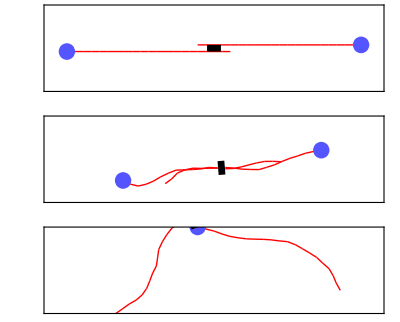

```mathematica
dir=fig1dir<>"/slide";
lks=pts[dir,"links"];
amots=pts[dir,"amotors"];
fs=draw[{},lks,amots,{},dir,False,{20,5},1,True, 21,Red,"movie",-1,1];
GraphicsColumn[fs[[{1,31,101}]],Spacings->10]
```

### E

Requires first running 
	txt2dat.py [fig1dir <> "/buckle/"] links
	txt2dat.py [fig1dir <> "/buckle/"] amotors
	txt2dat.py [fig1dir <> “/buckle/”] pmotors

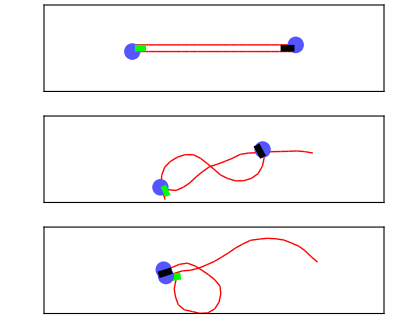

```mathematica
dir=fig1dir<>"/buckle";
lks=pts[dir,"links"];
amots=pts[dir,"amotors"];
pmots=pts[dir,"pmotors"];
fs=draw[{},lks,amots,pmots,dir,False,{20,5},1,True, 21,Red,"movie",-1,1];
GraphicsColumn[fs[[{1,31,101}]],Spacings->10]
```

## Figure 2

For these plots, you have to measure the wall clock time of the simulation. I did this with the following code, where $cmd was my simulation command (see versatile_framework_paper/README.md) and $data_dr was the “data” output directory of the simulation

startt = `date + % s`
./$cmd
endt = `date + % s`
tott = $ (echo $startt $endt | awk' {printf "%d", $2 - $1}')
echo $tott > "$data_dr/time.txt"

Once all the times are run, I make a fil

### A

#### Red Curve

```mathematica
dir=fig2dir<>"/npoly_arr";
ns={1,2,5,10,20,50,100,200,500,1000,2000,5000,10000,20000,50000};
dirs=Table[dir<>"/dens"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=ns*16+2*0.01*75^2;(*in paper, constant addition was off -- 4*0.1*75^2"*)
reddat={nparts,times}ᵀ;
```

#### Blue Curve

```mathematica
dir=fig2dir<>"/mdens_arr_lin";
ns={1,2,5,10,20,50,100,200,500,1000,2000,5000,10000};
denss=ns*0.001;
dirs=Table[dir<>"/dens"<>ToString[NumberForm[d,{3,3}]],{d,denss}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=500*16+denss*75^2;(*in paper, constant addition was off -- 4*0.1*75^2"*)
bluedat={nparts,times}ᵀ;
```

#### Black Curve

```mathematica
dir=fig2dir<>"/dens_arr_lin";
ns={1,2,5,10,20,50,100,200,500};
dirs=Table[dir<>"/dens"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=ns*16+2*0.1*ns*75^2;
blackdat={nparts,times}ᵀ;
```

```mathematica
ticksb=LogTicks[10,2,6];
tickst=LogTicks[10,2,6,ShowTickLabels->False];
ticksl=LogTicks[10,0,10];
ticksr=LogTicks[10,0,10,ShowTickLabels->False];
```

```mathematica
npartplt=Show[
ListPlot[
{Log10[reddat],Log10[bluedat],Log10[blackdat]},
PlotMarkers->{●,10},PlotStyle->{Red,Blue,Black},Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,tickst}},
PlotRange->{{1.5+Log10[2],6+Log10[1.5]},{0,5}},FrameLabel->{"# Particles","Wall Clock Time (s)"},
PlotLegends->Placed[PointLegend[{"ρ_motor const.","ρ_actin const."},LabelStyle->FontSize->18,LegendMarkerSize->{30,30},Spacings->0.1],{0.3,0.8}]],
Plot[{x-1,2x-7.5},{x,1,7},PlotStyle->{{Blue,Thick,Dashed},{Black,Thick,Dashed}}]];
```

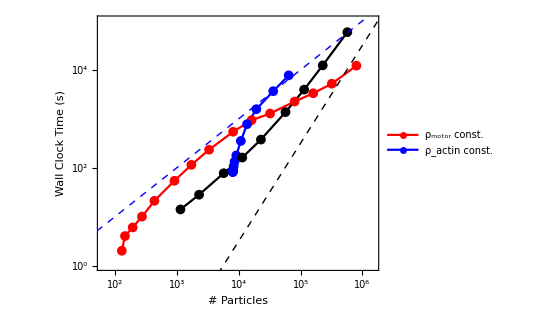

```mathematica
npartplt
```

### B

```mathematica
dir=fig2dir<>"/sys_size_arr";
ns=10Range[10];
dirs=Table[dir<>"/sz"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
szs=ns^2;
blackdat={szs,times}ᵀ;
```

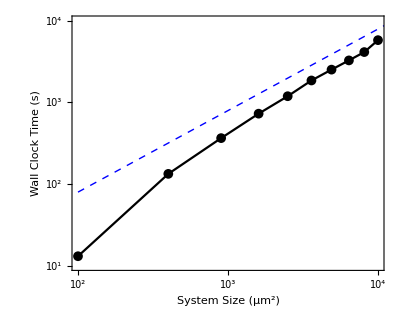

```mathematica
ticksb=LogTicks[10,1,4,TickLabelStep->0.25];
tickst=LogTicks[10,1,4,ShowTickLabels->False];
ticksl=LogTicks[10,0,4];
ticksr=LogTicks[10,0,4,ShowTickLabels->False];
szplt=Show[ListPlot[Log10[blackdat],PlotMarkers->{●,10},Axes->False,
PlotStyle->Black,Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,tickst}},
PlotRange->{Automatic,{1,4}},
FrameLabel->{"System Size (μm^2)","Wall Clock Time (s)"}],
Plot[{x-0.1},{x,2,5},PlotStyle->{{Blue,Thick,Dashed},{Red,Thick,Dashed}}]]
```

### C

```mathematica
dir=fig2dir<>"/grid_factor/";
ns=Join[{9},10Range[10],{200}];
gfs=ns*0.01;
dirs=Table[dir<>"gf"<>ToString[NumberForm[gf,{1,2}]],{gf,gfs}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
blackdat={gfs,times}ᵀ;
```

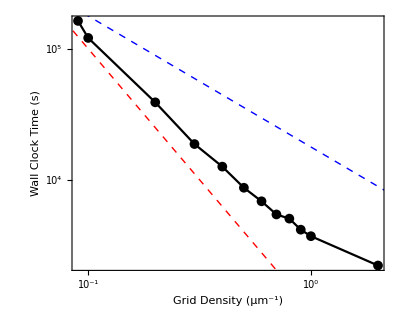

```mathematica
ticksb=LogTicks[10,-2,0,TickLabelStep->0.25];
tickst=LogTicks[10,-2,0,ShowTickLabels->False];
ticksl=LogTicks[10,3,6];
ticksr=LogTicks[10,3,6,ShowTickLabels->False];
gfplt=Show[ListPlot[Log10[blackdat],PlotMarkers->{●,10},Axes->False,
PlotStyle->Black,Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,tickst}},
PlotRange->Full,
FrameLabel->{"Grid Density (μm^-1)","Wall Clock Time (s)"}],
Plot[{-2x+3,-x+4.25},{x,-2,1},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick,Dashed}}]]
```

## Figures 3, S1

```mathematica
ClearAll[anglesT, anglesBwT, ccf,th2];
anglesT[rt_]:=ArcTan[rt[[All,3]],rt[[All,4]]];
anglesBwT[angs_]:=Map[(#-2Pi Floor[#/(2Pi)+0.5])&,angs[[2;;]]-angs[[1;;-2]]];
ccf[ths_]:=Module[{},
sums=Table[Accumulate[ths[[i;;]]],{i,Length[ths]}];
Table[Mean[Cos[sums[[1;;Length[sums]-i,i+1]]]],{i,0,Length[sums]-1}]
];
th2[ths_]:=Module[{},
sums=Table[Accumulate[ths[[i;;]]],{i,Length[ths]}];
Table[Mean[sums[[1;;Length[sums]-i,i+1]]^2],{i,0,Length[sums]-1}]
];
```

### 3 B

```mathematica
seeds=Range[100];
dir=fig3dir<>"/L200/";
dirs=Table[dir<>"seed"<>ToString[s],{s,seeds}];
lks=Table[pts[dr,"links"],{dr,dirs}];
angs=Map[anglesT,lks,{2}];
angsbw=Map[anglesBwT,angs,{2}];
ccfs=Map[ccf,angsbw,{2}];
th2s=Map[th2,angsbw,{2}];

muccf=Mean[Flatten[ccfs[[All,10;;]],1]];
muth2=Mean[Flatten[th2s[[All,10;;]],1]];
```

```mathematica
th2plt=Show[
ListPlot[muth2[[1;;50]],
FrameLabel->{"","","",Rotate[Style["⟨θ^2(ℓ)⟩",Blue],Pi]},
PlotMarkers->{Automatic,10},
PlotStyle->Blue,
FrameStyle->Blue,
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}}],
Plot[{x/20},{x,0,50},PlotStyle->{Thick,Dashing[Large],Blue}]
];
```

```mathematica
ccfplt=Show[
ListLogPlot[muccf[[1;;50]],
FrameLabel->{"ℓ (μm)",Style["⟨cosθ(ℓ)⟩",Red]},
FrameStyle->{{Red,Automatic},{Black,Black}},
Frame->{{True,False},{True,True}},
FrameTicks->{{All,None},{All,Automatic}},
PlotStyle->Red,
PlotMarkers->{Automatic,10}],
LogPlot[{Exp[-x/40]},{x,0,50},PlotStyle->{Thick,Dashing[Large],Red}]
];
```

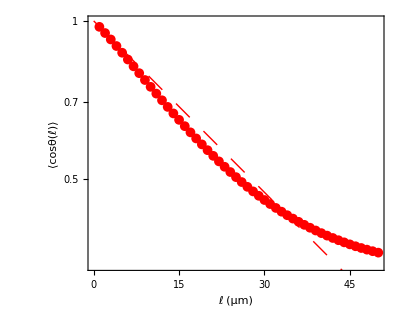
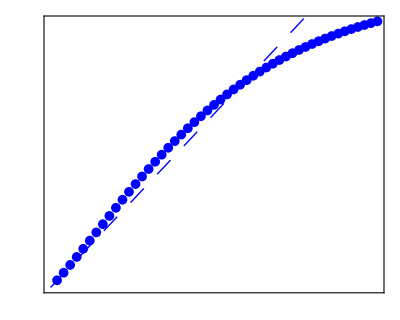

```mathematica
{ccfplt,th2plt}
```

### S1

```mathematica
dir=fig3dir<>"/decor_tf100/s34691004/";
lks=pts[dir,"links"];
angs=anglesT/@lks;
angsbw=anglesBwT/@angs;
ccs=Table[CorrelationFunction[angsbw[[All,i]],{0,19999}],{i,1,Length[angsbw[[1]]]}];
mccs=Mean[ccs];
cf={0.005(Range[Length[mccs]]-1),mccs}ᵀ;
decortimes=0.01Table[Total[mccs[[1;;i]]],{i,2,20000}];
```

#### S1A

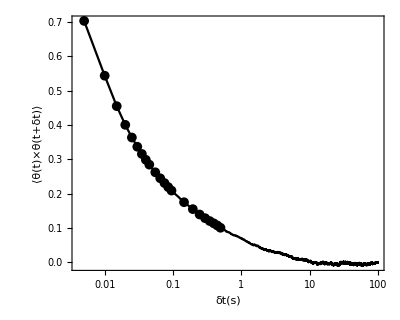

```mathematica
ps=Join[Range[10],Range[12,18,2],Range[2,10]10];
Show[
ListLogLinearPlot[cf,PlotRange->Full,Joined->True,PlotStyle->Black,FrameLabel->{"δt(s)",Style["⟨θ(t)×θ(t+δt)⟩",SingleLetterItalics->False]}],
ListLogLinearPlot[cf[[ps]],PlotRange->Full,PlotMarkers->{●,10},PlotStyle->Black]
]
```

#### S1B

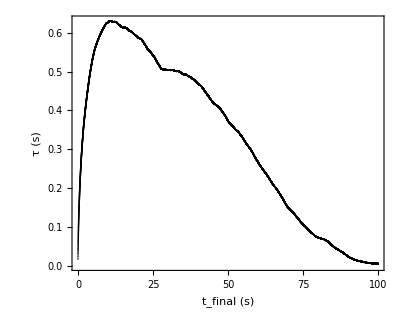

```mathematica
ListPlot[decortimes, PlotRange->Full,PlotStyle->{Black,Thick},DataRange->{0,100},FrameLabel->{"t_final (s)","τ (s)"}]
```

### 3 D

Postprocessing requirements :
(1) Change “actins” data from periodic boundaries to free boundaries with script versatile_framework_paper/python/periodic2definite.py
e.g,
python versatile_framework_paper/python/periodic2definite.py test actins 100 100
will generate the file test/actins_ext.txt which is the same simulation but with free boundaries. 
In this example, (100,100) are the width and height of the simulation, respectively (in μm).
(2) Get the endpoints of all the filaments in a dat file using the script versatile_framework_paper/python/txt2dat_ends.py. Same usage as txt2dat.py, but only keeps filament endpoints. Assumes a 21-bead filament, but can be changed by changing the 5th argument. See file for details. Example usage:
python versatile_framework_paper/python/txt2dat_ends.py test actins_ext
generates the file test/txt_stack/actins_ext.dat from the file test/txt_stack/actins_ext.txt.

```mathematica
seeds=Range[1,100];
dir=fig3dir<>"/L20_np100_short/";
dirs=Table[dir<>"seed"<>ToString[s],{s,seeds}];
actsext=ParallelTable[pts3[dr,"actins_ext"],{dr,dirs}];
evs=Table[Eigenvalues[Covariance[actsext[[All,t,i,1;;2]]]],{t,2,1001},{i,1,200}];
ts=Range[0.001,1,0.001];
maxevs=evs[[All,All,1]];
minevs=evs[[All,All,2]];
mumaxevs=Mean/@maxevs;
muminevs=Mean/@minevs;
sigmaxevs=StandardDeviation/@maxevs;
sigminevs=StandardDeviation/@minevs;
```

```mathematica
ticksx=LogTicks[10,-3,1];
fluctplt=Show[
ListPlot[Log10[{
{ts,mumaxevs/Max[mumaxevs]}ᵀ,
{ts,(mumaxevs-sigmaxevs)/Max[mumaxevs]}ᵀ,
{ts,(mumaxevs+sigmaxevs)/Max[mumaxevs]}ᵀ,
{ts,muminevs/Max[muminevs]}ᵀ,
{ts,(muminevs-sigminevs)/Max[muminevs]}ᵀ,
{ts,(muminevs+sigminevs)/Max[muminevs]}ᵀ
}],
PlotRange->Full,
PlotStyle->{Blue,Blue,Blue,Red,Red,Red},
PlotMarkers->{
{Graphics[{Blue,Disk[{0,0}]}],0.02},"-","-",
{Graphics[{Red,Disk[{0,0}]}],0.02},"-","-"},
Filling->{2->{3},5->{6}},
FrameLabel->{"t (s)","λ(t)/λ(1)"},
FrameTicks->{{ticksx,Automatic},{ticksx,Automatic}}
],
LogLogPlot[{t^{7/8}/1,t^{3/4}/0.9},{t,0.001,10},PlotStyle->{Blue,Red}]
];
```

```mathematica
fluctplt
```

-Graphics-

## Figure 4

### A

```mathematica
dir=fig3dir<>"/kb_arr_L200/s34691004/";
kbs=Join[Flatten[Outer[Times,10^Range[-3,-1],Range[9]]],{1}]; 
dirs=Table[dir<>"kb"<>ToString[NumberForm[N[kb],{1,3}]],{kb,kbs}];
lks=ParallelMap[pts[#,"links"]&,dirs];
angs=ParallelMap[anglesT,lks,{2}];
angsbw=ParallelMap[anglesBwT,angs,{2}];
thsqs=ParallelMap[th2,angsbw,{2}];
muth2s=Mean/@thsqs;
maxl=20;
fsmid=Table[LinearModelFit[muth2s[[i,1;;maxl]],x,x],{i,Length[muth2s]}];
msmid=D[Normal[#],x]&/@fsmid;
```

```mathematica
lplpplt=Show[ListLogLogPlot[{2*kbs/0.004,1/msmid}ᵀ[[10;;]],PlotMarkers->Automatic,PlotStyle->Black],LogLogPlot[x,{x,5,1000},PlotStyle->{Black,Dashing[0.05],Thick}],
FrameLabel->{"κ_B (k_BT×μm)","L_p(μm)"}];
```

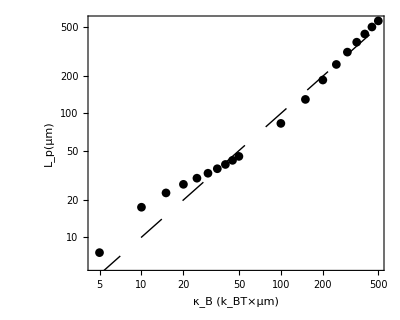

```mathematica
lplpplt
```

### B

```mathematica
dir=fig3dir<>"/kl_arr_L200/s34691004/";
kls=Join[Flatten[Outer[Times,10^{-2,-1,0,1,2},{1,2,5}]]];
dirs=dir<>"kl"<>ToString[NumberForm[N[#],{3,2}]]&/@kls;
lks=pts[#,"links"]&/@dirs;
angs=Map[anglesT,lks,{2}];
angsbw=Map[anglesBwT,angs,{2}];
thsqs=ParallelMap[th2,angsbw,{2}];
muth2s=Mean/@thsqs;
maxl=20;
fsmid=Table[LinearModelFit[muth2s[[i,1;;maxl]],x,x],{i,Length[muth2s]}];
msmid=D[Normal[#],x]&/@fsmid;
```

```mathematica
kllpplt=ListLogLogPlot[{kls[[1;;-2]],1/msmid[[1;;-2]]}ᵀ,PlotMarkers->Automatic,PlotStyle->Black,
FrameLabel->{"k_a (pN/μm)","L_p(μm)"},PlotRange->Full,Joined->True];
```

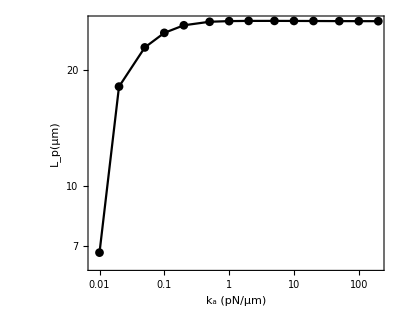

```mathematica
kllpplt
```

### C

```mathematica
dir=fig3dir<>"/nm_arr_L200/s34691004/";
nms=Join[Flatten[Outer[Times,10^{1,2,3},Range[9]]],{10000}];
dirs=dir<>"nm"<>ToString[#]&/@nms;
lks=ParallelMap[pts[#,"links"]&,dirs];
angs=ParallelMap[anglesT,lks,{2}];
angsbw=ParallelMap[anglesBwT,angs,{2}];
thsqs=ParallelMap[th2,angsbw,{2}];
muth2s=Mean/@thsqs;
lklengths=Sqrt[lks[[All,1,1,3]]^2+lks[[All,1,1,4]]^2];
maxl=20;
fsmid=Table[LinearModelFit[
{Range[0,Min[Length[muth2s[[i]]],maxl]-1]*lklengths[[i]],
muth2s[[i,1;;Min[Length[muth2s[[i]]],maxl]]]}ᵀ,x,x],{i,Length[muth2s]}];
msmid=D[Normal[#],x]&/@fsmid;
```

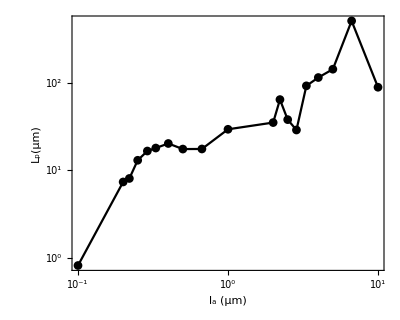

```mathematica
ticksx=LogTicks[10,-2,1];
ticksy=LogTicks[10,-1,3];
nmlpplt=ListPlot[Log10[{lklengths,1/msmid}ᵀ[[;;-9]]],PlotMarkers->Automatic,PlotStyle->Black,
FrameLabel->{"l_a (μm)","L_p(μm)"},PlotRange->Full,
FrameTicks->{{ticksy,Automatic},{ticksx,Automatic}},Axes->False,Joined->True
]
```

## Figures 5, S2

```mathematica
ClearAll[drawStretch];
drawStretch[actins_,links_,amotors_,pmotors_,dir_,movieFlag_,fov_:{500,500},dt_:1,acolor_:Red,cell_:{0,0},strainPct_:0,l0_:1,
colorByEnergy_:True,enghilo_:{0,0},scheme_:"BlueGreenYellow"]:=
Module[
{actinsr=actins, linksr=links,amotorsr=amotors,pmotorsr=pmotors},
(*Generate Image Time Series, make into movie*)
δrx=strainPct*fov[[1]]*cell[[2]];
cm=fov*cell;
minx=fov[[1]](cell[[1]]-0.5);
maxx=fov[[1]](cell[[1]]+0.5);
miny=fov[[2]](cell[[2]]-0.5);
maxy=fov[[2]](cell[[2]]+0.5);
frames={};
If[colorByEnergy,
If[enghilo[[1]]==enghilo[[2]],
engs=(Norm/@Flatten[links[[All,All,3;;4]],1]-l0);
cf=ColorData[{scheme,{Min[engs],Max[engs]}}],
cf=ColorData[{scheme,{enghilo[[1]],enghilo[[2]]}}]
],
cf[i_]:="Red"
];
If[actinsr≠{},
actinsr[[All,All,1;;2]]=Map[ (#+cm+{δrx,0})&,actinsr[[All,All,1;;2]],{2}];AppendTo[frames,Map[actin[#,Blend[{acolor,Red},Part[#,5]/10.]]&,actinsr,{2}]]];
If[linksr≠{},
linksr[[All,All,1;;2]]=Map[ (#+cm+{δrx,0})&,linksr[[All,All,1;;2]],{2}];
AppendTo[frames,Map[link[#,Abs[0.5fov[[1]]],cf[Abs[Norm[#[[3;;4]]]-l0]]]&,linksr,{2}]]
];
If[amotorsr≠{},
amotorsr[[All,All,1;;2]]=Map[(#+cm+{δrx,0})&,amotorsr[[All,All,1;;2]],{2}];
AppendTo[frames,Map[amotor,amotorsr,{2}]]];
If[pmotorsr≠{},
pmotorsr[[All,All,1;;2]]=Map[(#+cm+{δrx,0})&,pmotorsr[[All,All,1;;2]],{2}];AppendTo[frames,Map[pmotor,pmotorsr,{2}]]];
frames=Transpose[frames];
frames=Map[
Show[#,
Frame->True,
PlotRange->{{minx,maxx},{miny,maxy}},
Background->White,
(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)
FrameTicks->None,
Ticks->None,
BaseStyle->{FontSize->24,FontColor->Black}
]&
,frames
];
If[movieFlag, Export[dir<>"/data/movie.avi",frames]];
frames
];
```

### A

```mathematica
dir=fig5dir<>"kf1000/kcl1000.0";
```

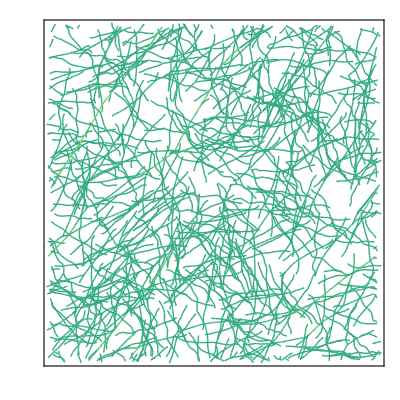
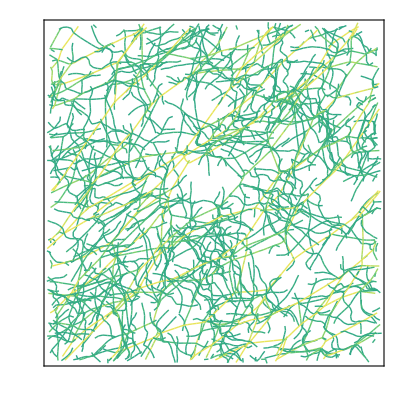
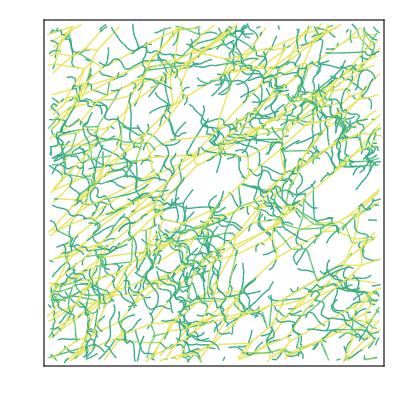

```mathematica
γs=Range[0.001,0.5,0.001];
lks=pts[dir,"links"];
s=0.5;
boxsz=75;
fov=boxsz{1,1};
pr=boxsz*{{-0.5,0.5},{-0.5,0.5}};
engs=(Norm/@Flatten[lks[[All,All,3;;4]],1]-1);
englims={-0.025,0.025};
fs0=drawStretch[{},{lks[[21]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
fs1=drawStretch[{},{lks[[51]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
fs2=drawStretch[{},{lks[[-1]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
{fs0,fs1,fs2}
```

### B

```mathematica
strain=Flatten[Table[ConstantArray[0.001*i,20],{i,1,500}]];
te=Total[Transpose[Import[dir<>"/data/pe.txt","TSV"]]];
rng0=Range[1,101];
rng0b=Range[1,101,5];
rng1=Range[2000,2100,5];
rng2=Range[5000,5100,5];
rng3=Range[8000,8100,5];
ClearAll[tickfcn];
tickfcn[min_,max_,nticks_:50,nlabels_:5]:=Table[{x,If[Mod[x nlabels/(max-min),1]==0,ToString[N[x]],""]},{x,min,max,(max-min)/(nticks)}]
ts=Range[0,.5,0.001];
strplt=ListPlot[{ts[[rng0]]*100,strain[[rng0]]}ᵀ,Joined->True,PlotStyle->{Black,Dashed,Thick},BaseStyle->FontSize->22,
FrameTicks->{{tickfcn[0.000,0.006,30,6],None},{(*tickfcn[0,10,50,5]*)All,Automatic}},FrameLabel->{Style["t-t_0(s)",SingleLetterItalics->False],"γ-γ_0","",""},AspectRatio->0.8,
Frame->{{True,False},{True,True}},
ImageSize->350];
p1=ListPlot[{ts[[rng0b]],te[[rng1]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{●,10},
FrameTicks->{{None,{58,60,62}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameStyle->{Thick,Blue}];
p2=ListPlot[{ts[[rng0b]],te[[rng2]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{■,10},
FrameTicks->{{None,{1320,1380,1440}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameLabel->{"","","",Style[Rotate["U_tot (pNμm)",Pi],Blue]},
FrameStyle->{Thick,Blue}];
p3=ListPlot[{ts[[rng0b]],te[[rng3]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{▲,10},
FrameTicks->{{None,{8800,8950,9100}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameStyle->{Thick,Blue}];
```

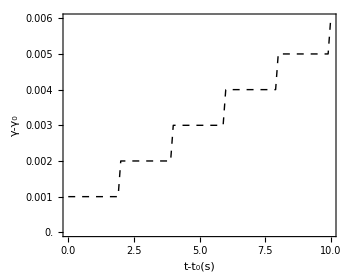
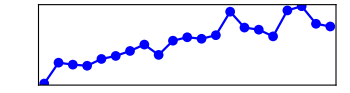
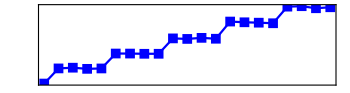
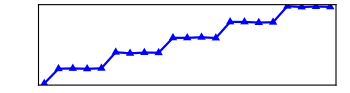

```mathematica
{strplt,p1,p2,p3}
```

### C

```mathematica
kls={0.1,0.2,0.5,1,2,5,10,20,50,100,200,500,1000};
dir=fig5dir<>"kf1000/";
dirs=dir<>"kcl"<>ToString[NumberForm[#,{2,1}]]&/@kls;
dt=10^(-6);
tfs=0.5;
engs=Transpose/@Table[Import[dr<>"/data/pe.txt","TSV"],{dr,dirs}];
te=Total/@engs;
ts=Range[0,0.49999,0.5/10000];
γs=Range[1,500]0.001;
eqengs=Table[Mean/@Partition[te[[i]],20],{i,Length[te]}];
dats=({γs[[1;;Length[#]]],#/75^2}ᵀ)&/@eqengs;
ClearAll[myplt];
myplt[dat_,title_,legtitle_,x10offset_:0,x15offset_:0,lgdIdxs_:All]:=
Show[
ListLogLogPlot[dat,
PlotStyle->"RustTones",
Frame->True,
FrameStyle->Black,
FrameLabel->{"γ","w (pN/μm)",title}
],
Plot[{2x+x10offset,7/2x+x15offset},{x,-4,10},PlotStyle->{{Blue,Dashed,Thick},{Darker[Green],Dashed,Thick}}],
BaseStyle->{FontFamily->"Arial",FontSize->22},
AspectRatio->0.8
];
```

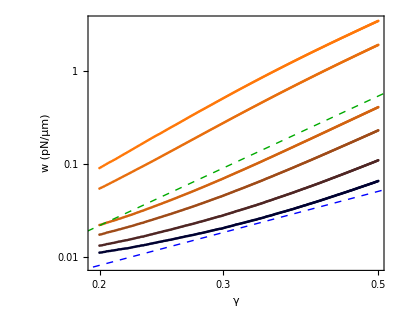

```mathematica
plt=myplt[dats[[{4,5,6,7,10,13},200;;]],"","k_cl [pN/μm]",-1.6,1.8,{4,5,6,7,10,13}]
```

### D (continued from C)

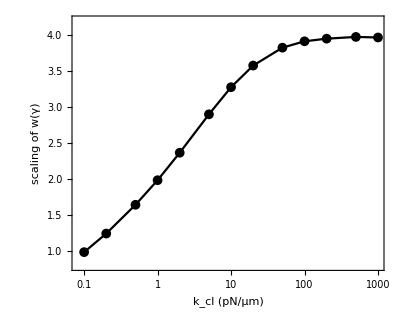

```mathematica
fs=Fit[#,{1,x},x]&/@Log[dats[[1;;,200;;]]];
exps=D[fs,x];
expdatsp={kls,exps}ᵀ;
ListLogLinearPlot[expdatsp,
PlotStyle->Black,
Frame->True,
FrameStyle->Black,
PlotRange->{0.8,4.2},
Joined->True,
PlotMarkers->{●,10},BaseStyle->FontSize->22,FrameLabel->{"k_cl (pN/μm)","scaling of w(γ)"},
AspectRatio->0.8]
```

### S2

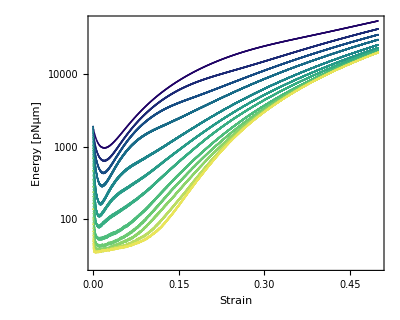

```mathematica
dir=fig5dir<>"k1000_strain_amp0.001";
nshears=Join[Flatten[Outer[Times,{1,10,100,1000},{2,5,10}]]];
dirs=Table[dir<>"/nbw"<>ToString[n],{n,nshears}];
dt=10^(-7);
tfs=500*dt*nshears;
δt=dt*1000;
engs=Transpose/@Table[Import[dr<>"/data/pe.txt","TSV"],{dr,dirs}];
te=Total/@engs;
ts=Table[Range[0,tf,Max[dt,tf/10000]],{tf,tfs}];
ts[[5]]=Range[0,tfs[[5]],tfs[[5]]/12500];
ls=Floor[Length/@ts,100];
eng1dat=Table[{ts[[i,;;ls[[i]]]],te[[i,;;ls[[i]]]]}ᵀ,{i,1,Length[ls]}];
dts=eng1dat[[All,2,1]]-eng1dat[[All,1,1]];
dshears=0.5/Length/@eng1dat;
eng2dat=Table[{ts[[i,;;ls[[i]]]]*dshears[[i]]/dts[[i]],te[[i,;;ls[[i]]]]}ᵀ,{i,1,Length[ls]}];
etplt2=ListLogPlot[eng2dat,PlotStyle->"BlueGreenYellow",FrameLabel->{"Strain","Energy [pNμm]"},PlotRange->{{0.001,0.5},Automatic}
]
```

## Figures 6, S3

### A

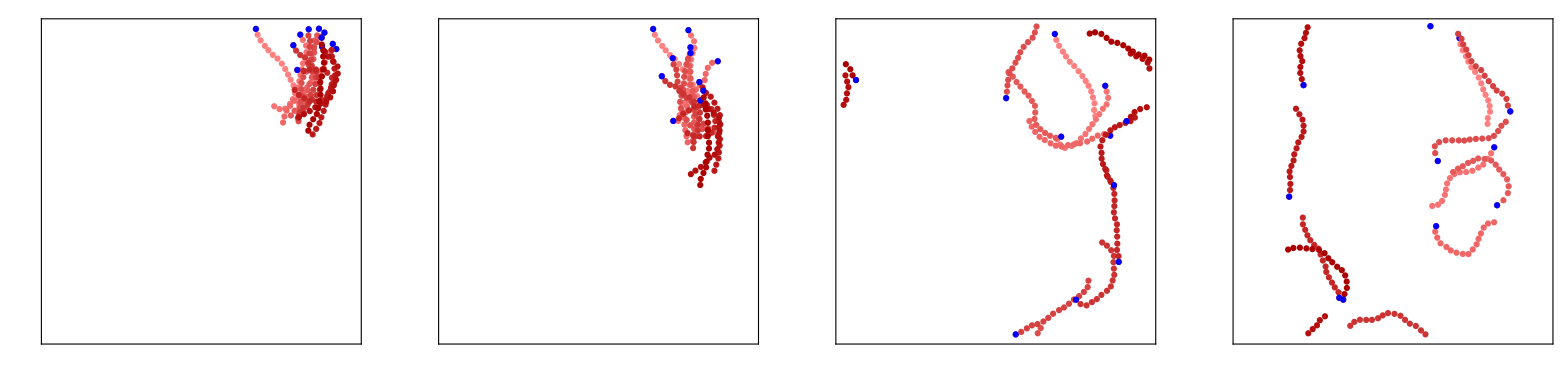

```mathematica
dir=fig6dir<>"/kon_arr_koff1/kon";
ks=Join[Flatten[Outer[Times,{0.001,0.01,0.1},{1,2,5}]],{1,2}];
dirs=dir<>ToString[NumberForm[#,{1,3}]]&/@ks;
konarr=pts[#,"actins"]&/@dirs;
maxf=401;
cf=ColorData[{"DeepSeaColors",{1,maxf}}];
cf2[i_]:=Blend[{Pink,Darker[Red]},(i-1)/(maxf-1)];
start=5;
fs=Table[
draw[
konarr[[j,{i+start}]],{},{},{},dirs[[-1]],False,25{{-1,1},{-1,1}},1,True,16,cf2[i]
],
{j,1,Length[konarr]},
{i,1,maxf,40}
];
pics=Show/@fs;
grow=GraphicsRow[pics[[{1,4,7,-2}]],Spacings->20];
grow
```

### B

#### Green

```mathematica
dir1=fig6dir<>"/dens_arr_kon1_koff1/mdens";
ρs=Join[Range[0.0,1,0.1],Range[2,8]];
dirs=dir1<>ToString[NumberForm[#,{3,1}]]&/@ρs;
lks1=Table[pts[dr,"links"],{dr,dirs}];
drs=lks1[[All,2;;-1,All,1;;2]]-lks1[[All,1;;-2,All,1;;2]];
drps1=Map[rijP[#,{50,50}]&,drs,{3}];
vs=Map[Norm[#]&,drps1,{3}];
norms=Map[Norm,lks1[[All,1;;-2,All,3;;4]],{3}];

rspar=lks1[[All,1;;-2,All,3;;4]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];

vspar=MapThread[Dot,{drps1,rspar},3];
vsperp=MapThread[Dot,{drps1,rsperp},3];

dt=0.5;
muvs=Mean/@Flatten/@vs/dt;
par1=Mean/@Flatten/@vspar/dt;
perp1=Sqrt[-par1^2+muvs^2];
```

#### Red Curve

```mathematica
dir2=fig6dir<>"/length_arr_kon1_koff1/nm";
nms=Join[Range[2,20],Range[22,50,2]];
dirs=dir2<>ToString[#]&/@nms;

lks2=Table[pts[dr,"links"],{dr,dirs}];

drs=lks2[[All,2;;-1,All,1;;2]]-lks2[[All,1;;-2,All,1;;2]];
drps2=Map[rijP[#,{50,50}]&,drs,{3}];
vs=Map[Norm[#]&,drps2,{3}];

norms=Map[Norm,lks2[[All,1;;-2,All,3;;4]],{3}];
vspar=Table[drps2[[i,t,j]].lks2[[i,t,j,3;;4]]/norms[[i,t,j]],{i,1,Length[drps2]},{t,1,Length[drps2[[i]]]},{j,1,Length[drps2[[i,t]]]}];
muvs=Mean/@Flatten/@vs/dt;

par2=Mean/@Flatten/@vspar/dt;
perp2=Sqrt[-par2^2+muvs^2];
```

#### Blue Curve

```mathematica
dir=fig6dir<>"/kon_arr_koff1/kon";
ks=Join[Flatten[Outer[Times,{0.001,0.01,0.1},{1,2,5}]],{1,2}];
dirs=dir<>ToString[NumberForm[#,{1,3}]]&/@ks;

lks3=Table[pts[dr,"links"],{dr,dirs}];

drs=lks3[[All,2;;-1,All,1;;2]]-lks3[[All,1;;-2,All,1;;2]];
drps3=Map[rijP[#,{50,50}]&,drs,{3}];
vs=Map[Norm[#]&,drps3,{3}];

norms=Map[Norm,lks3[[All,1;;-2,All,3;;4]],{3}];
vspar=MapThread[Dot,{drps3,lks3[[All,1;;-2,All,3;;4]]/norms},3];

muvs=Mean/@Flatten/@vs/dt;
par3=Mean/@Flatten/@vspar/dt;
perp3=Sqrt[-par3^2+muvs^2];
```

#### Whole Plot

```mathematica
rd0=0.5;
ρ0=4;
L0=15;
Lm=0.5;
koff0=1;
```

```mathematica
xvals1=ρs Lm L0 rd0;
xvals2=(ρ0 Lm(nms-1)) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0));
```

```mathematica
headers=Map[Style[#,FontSize->22,FontFamily->"Arial"]&,{{"ρ","L","r_D"},{"v_(||)","v_⊥"}},{2}];
legtable[pairs_]:=TableForm[
Partition[pairs,3]ᵀ,TableAlignments->Left,TableSpacing->{1,1},
TableHeadings->headers,Frame->True];
sz=10;
tab=
{{"","v_(||)","v_⊥"},
{"ρ_m",Graphics[{Green,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->sz]},
{"L",Graphics[{Red,Disk[{0,0},0.1]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Red]],White,Rectangle[]},ImageSize->sz]},
{"r_D",Graphics[{Blue,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Blue]],White,Rectangle[]},ImageSize->sz]}};
leg=Grid[tab,BaseStyle->{FontSize->19,FontFamily->"Arial"},Frame->All,Spacings->{0.2,0.2},Background->{{LightGray,None},{LightGray,None}}];
```

```mathematica
vplt1=ListPlot[
{{xvals1,par1}ᵀ,{xvals2,par2}ᵀ,{xvals3,par3}ᵀ,
{xvals1,perp1}ᵀ,{xvals2,perp2}ᵀ,{xvals3,perp3}ᵀ},Joined->True,
PlotMarkers->{{●,10},{●,10},{●,10},{□,15},{□,15},{□,15}},
PlotStyle->{Green,Red,Blue,Green,Red,Blue},PlotRange->{{0,20},{0,1.05}},
FrameLabel->{"ρ_ml_mLr_D","v(μm/s)"}];
```

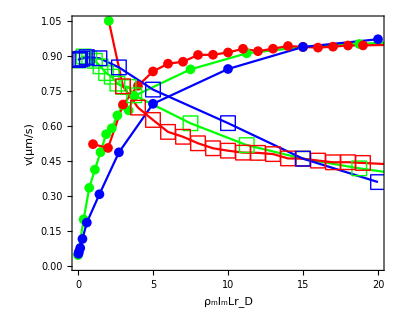
-Graphics- | v_(||) | v_⊥
ρ_m | -Graphics- | -Graphics-
L | -Graphics- | -Graphics-
r_D | -Graphics- | -Graphics-

```mathematica
vplt=Overlay[{vplt1,leg},Alignment->{-0.19,-0.29}]
```

### C (Continued from B)

```mathematica
ClearAll[msdp]
msdp[drs_]:=Module[{},
sums=Table[Accumulate[drs[[t;;]]],{t,Length[drs]}];
dx2s=sums[[All,All,1]]^2+sums[[All,All,2]]^2;
msd=Table[Mean[dx2s[[1;;-t,t]]],{t,1,Length[dx2s]}];
ClearAll[sums,dx2s];
msd
];
```

```mathematica
ms1=ParallelTable[msdp[drps1[[j,All,i]]],{j,1,Length[drps1]},{i,1,L0}];
ms2=ParallelTable[msdp[drps2[[j,All,i]]],{j,1,Length[drps2]},{i,1,nms[[j]]-1}];
ms3=ParallelTable[msdp[drps3[[j,All,i]]],{j,1,Length[drps3]},{i,1,L0}];
```

```mathematica
(*Sort MSD data sets by their xval*)
msddats1=Table[{xvals1[[i]],{Range[2000]*dt,Mean[ms1[[i]]]}ᵀ},{i,1,Length[ms1]}];
msddats2=Table[{xvals2[[i]],{Range[2000]*dt,Mean[ms2[[i]]]}ᵀ},{i,1,Length[ms2]}];
msddats3=Table[{xvals3[[i]],{Range[2000]*dt,Mean[ms3[[i]]]}ᵀ},{i,1,Length[ms3]}];
allmsddats=Sort[Join[msddats1,msddats2,msddats3]];
allxvals=allmsddats[[All,1]];
```

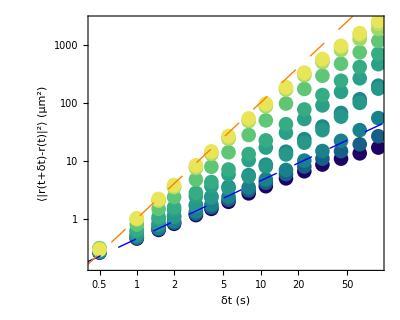

```mathematica
xidxs={2,4,5,6,7,8,10,20,30,40,50};
tidxs=Union[Round[10^Range[0,Log10[200],0.15]]];
logxvals=Log[allxvals[[xidxs]]];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
msdplt=Show[ListLogLogPlot[allmsddats[[xidxs,2,tidxs]],
PlotRange->Full,
PlotStyle->cf/@logxvals,
(*PlotStyle->(ColorData[{"BlueGreenYellow",Log[{allxvals[[1]],allxvals[[maxidx]]}]}][#]&/@Log[allxvals[[1;;maxidx;;didx]]]),*)
FrameLabel->{"δt (s)",Style["⟨|r(t+δt)-r(t)|^2⟩ (μm^2)",FontSize->20]},
PlotMarkers->ConstantArray[{●,15},6]
],
Plot[{x-0.8,2x},{x,-1,200},PlotStyle->{{Blue,Thick,Dashing[Large]},{Orange,Thick,Dashing[Large]}}]
]
```

### S3 (Continued from B)

```mathematica
(*Function for getting the end-to-end vector for all links in a time series with one filament*)
e2ev[lks_,fov_]:=
Map[
rijP[
rijP[#[[-1,1;;2]]+#[[-1,3;;4]],fov]
-#[[1,1;;2]],fov
]&,
lks,{1}];
(*Vector Autocorrelation Function*)
vac[vs_]:=Module[{},
v0vt=Table[vs[[t]].vs[[t+dt]],{t,Length[vs]},{dt,0,Length[vs]-t}];
ac=Table[Mean[v0vt[[1;;-t,t]]],{t,1,Length[v0vt]}];
avgv0Sq=Mean[vs[[All,1]]]^2+Mean[vs[[All,2]]]^2;
avgV0sq=Mean[vs[[All,1]]^2+vs[[All,2]]^2];
(ac-avgv0Sq)/(avgV0sq-avgv0Sq)
];
```

```mathematica
e2e1=Map[e2ev[#,{50,50}]&,lks1];
e2e2=Map[e2ev[#,{50,50}]&,lks2];
e2e3=Map[e2ev[#,{50,50}]&,lks3];
e2ecc1=ParallelTable[vac[e2e1[[j]]],{j,1,Length[e2e1]}];
e2ecc2=ParallelTable[vac[e2e2[[j]]],{j,1,Length[e2e2]}];
e2ecc3=ParallelTable[vac[e2e3[[j]]],{j,1,Length[e2e3]}];
```

#### A

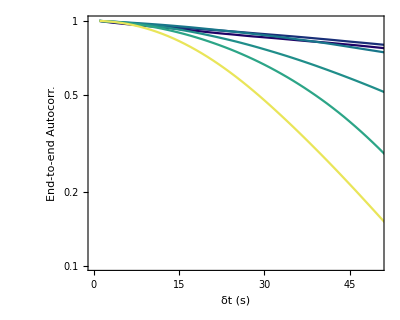

```mathematica
tidxs=Range[1,100];
xidxs=Range[1,Length[xvals1]];
xidxs={1,2,5,7,10,15};
logxvals=Log[xvals1[[xidxs]]+1];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
e2eccplt=ListLogPlot[e2ecc1[[xidxs,tidxs]],
PlotRange->{{0,50},{0.1,1}},
PlotStyle->cf/@logxvals,
Joined->True,
FrameLabel->{"δt (s)",Style["End-to-end Autocorr.",FontSize->20]}
]
```

#### C

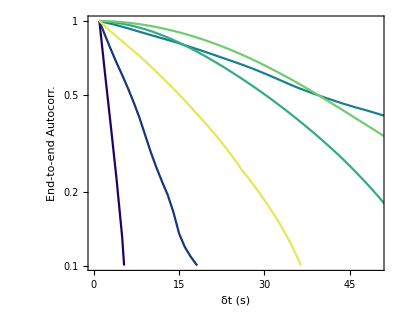

```mathematica
tidxs=Range[1,100];
xidxs={1,2,5,10,20,34};
logxvals=Log[xvals2[[xidxs]]+1];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
e2eccplt=ListLogPlot[e2ecc2[[xidxs,tidxs]],
PlotRange->{{0,50},{0.1,1}},
PlotStyle->cf/@logxvals,
Joined->True,
FrameLabel->{"δt (s)",Style["End-to-end Autocorr.",FontSize->20]}
]
```

#### B

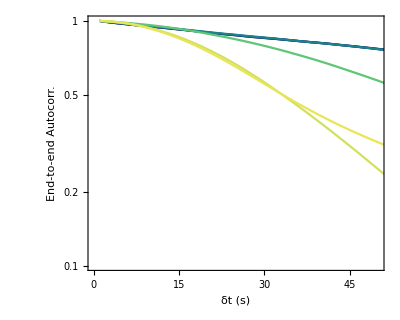

```mathematica
tidxs=Range[1,500];
xidxs={1,2,4,7,10,11};
logxvals=Log[xvals3[[xidxs]]];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
e2eccplt=ListLogPlot[e2ecc3[[xidxs,tidxs]],
PlotRange->{{0,50},{0.1,1}},
PlotStyle->cf/@logxvals,
Joined->True,
FrameLabel->{"δt (s)",Style["End-to-end Autocorr.",FontSize->20]}
]
```

### D (Continued from S3)

```mathematica
tf=50;
t1=Map[Total[#[[1;;tf]]]*dt&,e2ecc1];
t2=Map[Total[#[[1;;tf]]]*dt&,e2ecc2];
t3=Map[Total[#[[1;;tf]]]*dt&,e2ecc3];
```

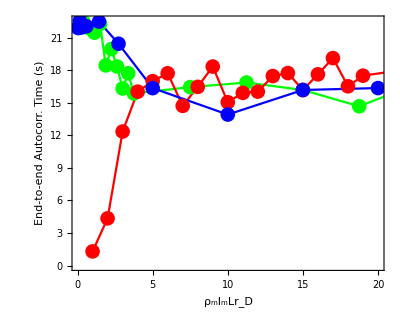

```mathematica
scplt=ListPlot[{{xvals1,t1}ᵀ[[2;;]],{xvals2,t2}ᵀ,{xvals3,t3}ᵀ},Joined->True,PlotRange->{{0.03,20},(*{-0.1,0}*)Automatic},PlotMarkers->{●,15},
PlotStyle->{Green,Red,Blue},FrameLabel->{"ρ_ml_mLr_D","End-to-end\nAutocorr. Time (s)"}]
```

## Figure 7, S4

### A

```mathematica
dir=fig7dir;
links=pts[dir,"links"];
ams=pts[dir,"amotors"];
pms=pts[dir,"pmotors"];
idxs={1,21,51,200};
frs=draw[{},links[[idxs]],ams[[idxs,1;;-1;;2]],pms[[idxs,1;;-1;;10]],dir,False,{50,50},1,False,16];
GraphicsRow[frs]
```

### B

```mathematica
rdf[acts_,fov_,δr_,maxr_,sampPairs_]:=Module[{},
rs=Range[0,maxr,δr];
rsmid=(rs[[2;;]]+rs[[;;-2]])0.5;
norms=2Pi δr rsmid Length[sampPairs]/(fov[[1]]*fov[[2]]);
rdft=
Table[
BinCounts[
Map[
Norm[rijP[#,fov]]&,
acts[[t,sampPairs[[All,1]],1;;2]]-acts[[t,sampPairs[[All,2]],1;;2]]],
{0,maxr,δr}]/norms,
{t,Length[acts]}
];
rdft
];
```

```mathematica
nm=11;
nparts=500*nm;
rngs=Table[Join[Range[1,nm i],Range[nm(i+1)+1,nparts]],{i,0,nparts/nm-1}];
(*All pairs of actin beads that are not on the same filament*)
allPairs=Union[Sort/@Flatten[
Table[{i,j},
{i,nparts},
{j,RandomSample[rngs[[Quotient[i-1,nm]+1]],1000]}],1]];
(*A sample of them*)
sampPairs=RandomSample[allPairs,500*499/2];
idxs={1,21,51,101,200};
acts=pts[fig7dir,"actins"];
gr=rdf[acts[[idxs]],{50,50},0.05,5,sampPairs];
cf=ColorData[{"BlueGreenYellow",Log10[{1,201}]}];
ts=idxs-1;
```

```mathematica
grplot=ListPlot[gr,PlotStyle->Table[{cf[Log10[t+1]],Thick},{t,ts}],FrameLabel->{"distance (μm)","radial distr. func."},Joined->True,PlotRange->Full,PlotLegends->Placed[SwatchLegend[ts,LegendLabel->"time (s)",LegendMarkerSize->20,Spacings->0,LegendLayout->"ReversedColumn"],{0.75,0.6}],DataRange->{0.025,4.975}]
```

### C

C,D, and S4 require you to have run the Python divergence calculating code "versatile_framework_paper/python/div_by_vbin.py"  described in section S4 of the paper. The command to run is
python versatile_framwork_paper/python/div_by_vbin.py [fig7dir]
there are lots of parameters you can toy with, to see them enter
python versatile_framework_paper/python/div_by_vbin.py --help
For the rest of the figures I used the output with the default parameter choices: 
fov = [50,50]
rbfunc = ‘gaussian’
rbeps = 5
dr = [1,1]
dt = 10
padding = 1
nbins = 10
minpts = 10
div_lsc = 10

```mathematica
vf50=Import[fig7dir<>"/analysis/xyuvd_nbins10_lsc10/t40.txt","TABLE"];
xyuv={vf50[[All,1;;2]],vf50[[All,3;;4]]}ᵀ;
xyd=vf50[[All,{1,2,5}]];
ldp=ListDensityPlot[xyd,PlotRange->25{{-1,1},{-1,1}},
ColorFunction->ColorData[{"ThermometerColors",{0.03,-0.03}}],ColorFunctionScaling->False,InterpolationOrder->1,FrameTicksStyle->White];
lvp=ListVectorPlot[xyuv,PlotRange->25{{-1,1},{-1,1}},Background->None];
mylvpd=Overlay[{ldp,lvp}]
```

### S4

#### S4B

```mathematica
vfs=Table[Import[fig7dir<>"/analysis/xyuvd_nbins10_lsc10/t"<>ToString[t]<>".txt","TABLE"],{t,Range[0,189]}];
lsc2=10;
vftg=Table[GroupBy[vfs[[t]],Round[#[[1;;2]],lsc2]&],{t,Length[vfs]}];
divst=Table[Total[vftg[[t,g,All,5]]],{t,Length[vftg]},{g,Length[vftg[[t]]]}];
divstr=divstᵀ;
minb=Position[divstr,Min[divstr]][[1,1]];
maxb=Position[divstr,Max[divstr]][[1,1]];
rmin=Union[Flatten[Round[vftg[[All,minb,All,1;;2]],lsc2],1]][[1]];
rmax=Union[Flatten[Round[vftg[[All,maxb,All,1;;2]],lsc2],1]][[1]];
```

```mathematica
diffbinsplt=ListPlot[divstr[[{minb,maxb}]]*1000/lsc2^2,Joined->True,PlotStyle->{Black,Red,Cyan},PlotRange->Automatic,FrameLabel->{"time (s)", "⟨∇·v_local⟩ (mHz)"},
PlotLegends->Placed[LineLegend[ToString/@{rmin,rmax},LegendLabel->Placed["Box Center",Top],Spacings->0,LabelStyle->FontSize->20],{0.6,0.8}]]
```

#### S4C (Continuing from S4B)

```mathematica
edges=Range[-30,30,5];
bins=(edges[[2;;]]+edges[[;;-2]])*0.5;
bcs=Table[BinCounts[divstr[[All,t]]*10,{edges}],{t,Length[divstr[[1]]]}];
difftimesplt=ListPlot[{bins,#/Total[#]}ᵀ&/@{bcs[[1]],bcs[[21]],bcs[[51]]},Joined->True,PlotRange->{Automatic,{-0.02,0.53}},PlotStyle->{Red,Blue,Green},PlotMarkers->{●,15},FrameLabel->{ "⟨∇·v_local⟩ (mHz)","prob."},
PlotLegends->Placed[PointLegend[{0,20,50},LegendLabel->"time (s)",Spacing->0,LabelStyle->FontSize->22,LegendMarkerSize->20],{0.8,0.6}]]
```

### D

```mathematica
ClearAll[filstrain];
filstrain[acts_,fov_:{50,50},nparts_:500]:=
Map[
Norm[
rijP[#,fov]]&,
acts[[All,Length[acts[[1]]]/nparts;;-1;;Length[acts[[1]]]/nparts,1;;2]]-acts[[All,1;;-1;;Length[acts[[1]]]/nparts,
1;;2]],
{2}];
L0=10;
acts=pts[fig7dir,"actins"];
s1=filstrain[acts];
drt=1-Mean/@s1/L0;
dlf=MovingAverage[(Min/@divst)/(Max/@divst),5];
```

```mathematica
lp1=ListPlot[dlf,Joined->True,PlotStyle->Blue,PlotRange->{-2,-0.4},
FrameStyle->{{Blue,Black},{Black,Black}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{"time (s)",Style["Min[∇·v_local] / Max[∇·v_local]",FontSize->20]},
ImagePadding->100,
ImageSize->500];
lp2=ListPlot[drt[[1;;Length[dlf]]],Joined->True,PlotRange->Full,
PlotStyle->Red,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Red,Red},{Black,Black}},
FrameLabel->{"","filament strain","",""},
ImagePadding->100,
ImageSize->500];
divstrplt=Overlay[
{Show[lp1,Frame->{{True,False},{True,True}}],
Show[lp2,Frame->{{False,True},{False,False}},
FrameTicks->All,
FrameLabel->{"","","",Rotate["filament strain",Pi]}]}]
```